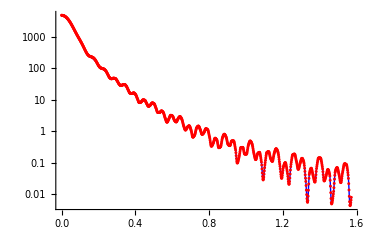

{{# 20250604_161352},{# primespec:	data/examplescenario/primaryspec/spec_20250219_132655_006/spectr.txt},{# qmax:	4},{# ma:	0.331859},{# mb:	0.14},{# mc:	0.14},{# [=>] pabc:	0.0890651},{# [=>] Eabc:	0.16593},{# B:	1},{# Q:	1},{# epsrel:	1e-05},{# epsabs:	0},{# iter:	10000}}

{pT,decayspec}

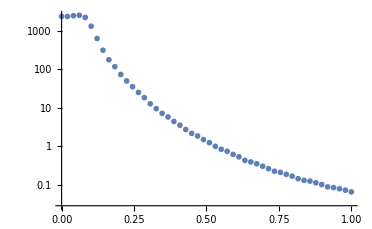

```mathematica
ClearAll["Global`*"]

primarydata=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/data/examplescenario/decayspec/decay_20250604_161352_005/primespec.txt"],"CSV"];
primarykeys=primarydata[[2]];
primarydata=primarydata[[3;;]];
qs=(Transpose@primarydata)[[1]];
primaryspec=(Transpose@primarydata)[[2]];

logprimespecfunc=Interpolation[Transpose@{qs,Log[primaryspec]}];
primespecfunc[x_]=If[x<Max[qs],Exp[logprimespecfunc[x]],0];
Show[
LogPlot[primespecfunc[x],{x,0,Max[qs]},PlotStyle->{Blue,Thick}],
ListLogPlot[Transpose@{qs,primaryspec},PlotStyle->{Red},PlotMarkers->{Automatic,3}]
]

decaydata=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/data/examplescenario/decayspec/decay_20250604_161352_005/decayspec.txt"],"CSV"];
decaycomments=decaydata[[;;13]]
decaykeys=decaydata[[14]]
decaydata=decaydata[[15;;]];
pTs=(Transpose@decaydata)[[1]];
decayspec=(Transpose@decaydata)[[2]];
ListLogPlot[Transpose@{pTs,decayspec}]
```

```mathematica
Clear[ma,mb,Eabc,B,Q]

w[p_,m_]=Sqrt[p*p+m*m];
ustar[t_,v_,p_]=(ma*Eabc+Q*p*t*v)/(w[t*Q,ma]*w[p,mb]);

s=Solve[1==ustar[t,v,p],v];
v1[t_,p_]=v/.s[[1]]//FullSimplify;
t1min[p_]=t/.Solve[0==D[v1[t,p],t],t][[2]]//FullSimplify;
vmin[p_]=v1[t1min[p],p]//FullSimplify;
s2=Solve[1==v1[t,p],t]//FullSimplify;
tmin[p_]=t/.s2[[1]]//FullSimplify;
tmax[p_]=t/.s2[[2]]//FullSimplify;
Print["v(t,p)|u==1:",v1[t,p], "(=:v1(t,p))"]
Print["v1=min(v1(t,p) at t=",t1min[p]]
Print["min(v1(t,p))=",vmin[p]]
Print["tmin(p)=",tmin[p]]
Print["tmax(p)=",tmax[p]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

v(t,p)|u==1:(-Eabc ma+√(mb^2+p^2) √(ma^2+Q^2 t^2))/(p Q t)(=:v1(t,p))

v1=min(v1(t,p) at t=(√(ma^2 (-Eabc^2+mb^2+p^2)))/(Eabc Q)

min(v1(t,p))=(Eabc (-Eabc ma+√(mb^2+p^2) √((ma^2 (mb^2+p^2))/Eabc^2)))/(p √(ma^2 (-Eabc^2+mb^2+p^2)))

tmin(p)=(Eabc ma p-√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

tmax(p)=(Eabc ma p+√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

0.0890651

0.16593

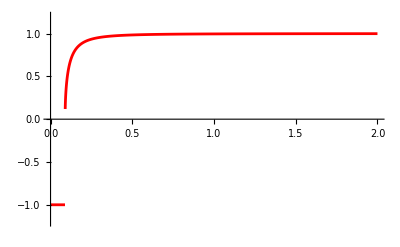

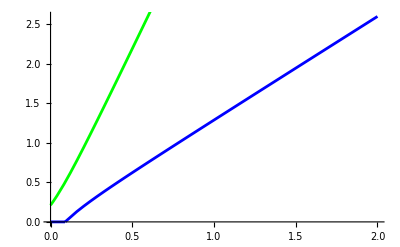

```mathematica
ma=0.331859;
mb=0.14;
mc=mb;
pabc=1/(2ma)√(((ma+mb)^2-mc^2)((ma-mb)^2-mc^2))
Eabc=√(mb^2+pabc^2)
B=1;
Q=1;

LowerBoundV[p_]=If[Eabc^2<mb^2+p^2,vmin[p],-1];
BetterLowerBoundV[t_,p_]=Clip[v1[t,p],{-1,1}];
LowerBoundT[p_]=If[tmin[p]<0,0,tmin[p]];

Plot[LowerBoundV[p],{p,0,2},PlotRange->{Automatic,{-1.2,1.2}},PlotStyle->Red]
Show[
Plot[LowerBoundT[p],{p,0,2},PlotStyle->Blue],
Plot[tmax[p],{p,0,2},PlotStyle->Green]
]

Manipulate[
(*RegionPlot[LowerBoundT[p]<t&&BetterLowerBoundV[t,p]<v<1,{t,-0.1*tmax[p],1.1*tmax[p]},{v,LowerBoundV[p]-0.1*Abs[1-LowerBoundV[p]],1+0.1*Abs[1-LowerBoundV[p]]}],
{p,0.0001,2},*)
RegionPlot[LowerBoundT[p]<t&&BetterLowerBoundV[t,p]<v<1,{t,-0.1*tmax[p],1.1*tmax[p]},{v,-1.1,1.1}],
{p,0.0001,2}
]
```

```mathematica
Install[StringJoin[ParentDirectory@NotebookDirectory[],"/Cuba-4.2.2/Cuhre"]](*be sure to "chmod 755 /Cuba-4.2.2/Cuhre" in order to use it*)
```

LinkObject[…]

```mathematica
Integrand[t_,v_,p_]=If[ustar[t,v,p]>1,primespecfunc[Q*t]*1/(√(ustar[t,v,p]^2-1))*1/(√(1-v^2))*t/(w[p,ma]*w[t*Q,mb]),0];
MyIntegral[p_]:=(ma*B*Q^2)/(p*π)*Cuhre[Integrand[t,v,p],{t,LowerBoundT[p],tmax[p]},{v,BetterLowerBoundV[t,p],1},Verbose->0][[1]][[1]];
pTstest=Array[#&,50,{0.001,1}]
```

{0.001,0.0213878,0.0417755,0.0621633,0.082551,0.102939,0.123327,0.143714,0.164102,0.18449,0.204878,0.225265,0.245653,0.266041,0.286429,0.306816,0.327204,0.347592,0.36798,0.388367,0.408755,0.429143,0.449531,0.469918,0.490306,0.510694,0.531082,0.551469,0.571857,0.592245,0.612633,0.63302,0.653408,0.673796,0.694184,0.714571,0.734959,0.755347,0.775735,0.796122,0.81651,0.836898,0.857286,0.877673,0.898061,0.918449,0.938837,0.959224,0.979612,1.}

```mathematica
decayspectest=Map[MyIntegral,pTstest];
```

Cuhre::accuracy: Desired accuracy was not reached within 50115 function evaluations on 386 subregions.

General::stop: Further output of Cuhre::accuracy will be suppressed during this calculation.

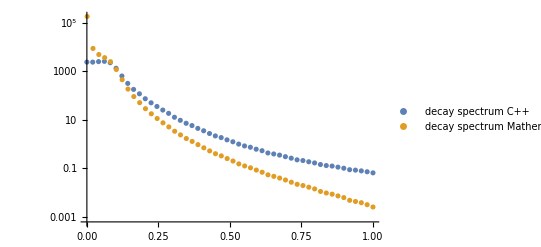

```mathematica
ListLogPlot[{Transpose@{pTs,decayspec},Transpose@{pTstest,decayspectest}},PlotLegends->{"decay spectrum C++","decay spectrum Mathematica"}]
```